```mathematica
$Assumptions=Γ>=0&&Element[Γ,Reals]&&t>=0&&Element[t,Reals]&&J>=0&&Element[J,Reals];
```

```mathematica
x={{0,1},{1,0}};
y={{0,-I},{I,0}};
z={{1,0},{0,-1}};
i=IdentityMatrix[2];
X1X2=KroneckerProduct[x,x];
Y1Y2=KroneckerProduct[y,y];
Z1Z2=KroneckerProduct[z,z];
Id=IdentityMatrix[4];
```

```mathematica
sigP={{0,1},{0,0}};
sigM={{0,0},{1,0}};
sigP1=KroneckerProduct[sigP,i];
sigM1=KroneckerProduct[sigM,i];
sigP2=KroneckerProduct[i,sigP];
sigM2=KroneckerProduct[i,sigM];
```

```mathematica
vec[op1_,op2_]:=KroneckerProduct[Transpose[op2], op1];
```

```mathematica
veccom[op_]:=vec[op, Id]-vec[Id,op];
```

```mathematica
D1=vec[sigP1,sigM1]-1/2 vec[sigM1.sigP1,Id]-1/2 vec[Id,sigM1.sigP1];
D2=vec[sigP2,sigM2]-1/2 vec[sigM2.sigP2,Id]-1/2 vec[Id,sigM2.sigP2];
```

```mathematica
L[J_,Γ_]:=-I J(veccom[X1X2]+veccom[Y1Y2])+Γ(D1+D2);
```

```mathematica
d=4;
Eij[i_,j_]:=SparseArray[{{i+1,j+1}->1},{d,d}];
Choi[S_]:=(1/d )*Simplify@Sum[KroneckerProduct[Eij[i,j],IdentityMatrix[d]].S.KroneckerProduct[IdentityMatrix[d],Eij[i,j]],{i,0,d-1},{j,0,d-1}];
```

## Measure ZZ symmetry

```mathematica
SuperZZ = vec[Z1Z2,Z1Z2];
S=MatrixExp[L[J,Γ]];
choiZZ=Choi[S.SuperZZ];
ZZchoi=Choi[SuperZZ.S];
1/2 Simplify[Tr[ConjugateTranspose[ZZchoi-choiZZ].(ZZchoi-choiZZ)]]
```

0

## Measure XX symmetry

```mathematica
SuperXX = vec[X1X2,X1X2];
S=MatrixExp[L[J,Γ t]];
choiXX=Choi[S.SuperXX];
XXchoi=Choi[SuperXX.S];
sXX=1/2 FullSimplify[Tr[ConjugateTranspose[XXchoi-choiXX].(XXchoi-choiXX)]]
```

(ⅇ^(-2 t Γ) (-t^2 Γ^2 Cos[4 J]-16 J^2 Cosh[t Γ]+(16 J^2+t^2 Γ^2) Cosh[2 t Γ]))/(2 (16 J^2+t^2 Γ^2))

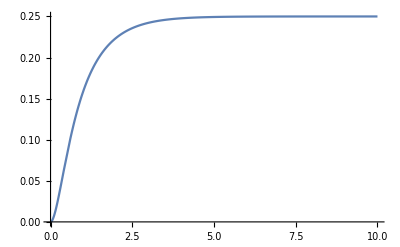

```mathematica
Plot[sXX/.{J->1,t->1}, {Γ,0,10} , PlotRange->{0,0.25}]
```